```mathematica
Quit
```

The notebook presents numerical checks of the analytic solutions for trajectories available in AnalyticSpinOrbitsHamiltonJacobi against numerical solutions of the equations of motion in first order form.  See arXiv:2603.04682  (https://arxiv.org/abs/2603.04682 )

PREREQUISITEs: the following packages are neededS
- KerrGeodesics from the BPToolkit. This package is needed to calculate the location of the geodesic separatrix.

If you make use of this notebook, please acknowledge 
- “Piovano”  (https://arxiv.org/abs/2603.04682 )
- KerrGeodesics package,  (https://zenodo.org/records/8108265 ) of the  BHPToolkit

NOTE: the shift to the radial trajectory δr[r_g] in all plunges includes a term proportional to δΥ_r/Υ_rg to ensure that the velocities and trajectories for critical plunge matches periodic orbits near the separatrix (e.g. in the limits r_(3g)->r_(2g)). 
To account for such a term, the ODEs are shifted by a term proportional to δΥ_r/Υ_rg.

### Convention for EoM

Here we follow the same convention of  CQG, Volume 37, Number 14  (https://iopscience.iop.org/article/10.1088/1361-6382/ab79d5 )

r_1== p/(1-e)
r_2== p/(1+e)
z_1==√(1-x^2)

or

p==2(r_1 r_2)/(r_1+r_2)
e== (r_1-r_2)/(r_1+r_2)
x ==  Sign[ℒ]√(1-z_1^2)

(circular) 0<e<1 (parabolic)
(retrograde) -1 < x < 1 (prograde)
p> p_LSO(e,x)

Equatorial orbits

x==±1
z_1==0
𝒬 ==0

“spar” and “sort” are the parallel and orthogonal component of the spin to the total angular momentum.

### Loading all the necessary files

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<KerrGeodesics`
```

```mathematica
Get["../AnalyticSpinOrbitsHamiltonJacobi.wl"]
```

## Generic plunge

## Regular gauge - prograde

### Calculation orbits

IMPORTANT NOTE: the input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aPlunge=0.9`50;
eccPlunge=0.7`50;
xPlungeBoundOrbit=1;
```

```mathematica
pPlunge=KerrGeoSeparatrix[aPlunge,eccPlunge,xPlungeBoundOrbit]-1
```

2.0782127178009769707291085222982272524218364585

```mathematica
rp=1+√(1-aPlunge^2);
rm=1-√(1-aPlunge^2);
```

```mathematica
corrPlunge=KerrNearEqSpinOrbitCorrFEPlunge[aPlunge,pPlunge,eccPlunge,xPlungeBoundOrbit];
```

```mathematica
r1g=pPlunge/(1-eccPlunge);
```

### Numerical solutions equations of motion vs analytic results

```mathematica
δrODEPlunge=δr/.First@NDSolve[{δr'[r]==corrPlunge["δvrpar"][r]/corrPlunge["vrg"][r]-corrPlunge["δΥrhat"],δr[r1g-10^(-10)]==corrPlunge["δrpar"][r1g-10^(-10)]},δr,{r,1/100,r1g-10^(-10)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

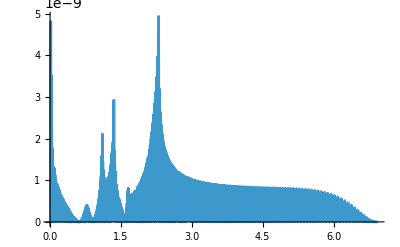

```mathematica
Plot[Abs[δrODEPlunge[r]-corrPlunge["δrpar"][r]],{r,1/100,r1g},PlotRange->All]
```

```mathematica
δtODEPlunge=δt/.First@NDSolve[{δt'[r]==-(corrPlunge["δvtpar"][r]-corrPlunge["δΥrhat"]corrPlunge["vtg"][r])/corrPlunge["vrg"][r],δt[r1g-10^(-10)]==corrPlunge["δtpar"][r1g-10^(-10)]},δt,{r,rp+10^(-3),r1g-10^(-10)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

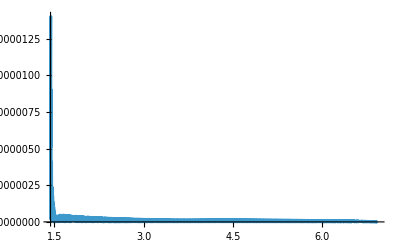

```mathematica
Plot[Abs[δtODEPlunge[r]-corrPlunge["δtpar"][r]],{r,rp+10^(-3),r1g-10^(-10)},PlotRange->All]
```

```mathematica
δϕODEPlunge=δϕ/.First@NDSolve[{δϕ'[r]==-(corrPlunge["δvϕpar"][r]-corrPlunge["δΥrhat"]corrPlunge["vϕg"][r])/corrPlunge["vrg"][r],δϕ[r1g-10^(-10)]==corrPlunge["δϕpar"][r1g-10^(-10)]},δϕ,{r,rp+10^(-3),r1g-10^(-10)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

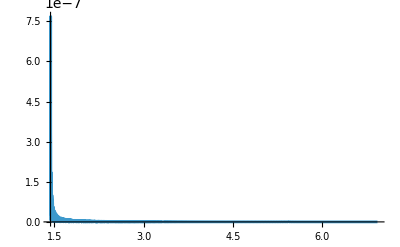

```mathematica
Plot[Abs[δϕODEPlunge[r]-corrPlunge["δϕpar"][r]],{r,rp+10^(-3),r1g},PlotRange->All]
```

## Regular gauge - retrograde

### Calculation orbits

IMPORTANT NOTE: the input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aPlungeBoundOrbit=0.9`55;
eccPlungeBoundOrbit=0.7`55;
xPlungeBoundOrbit=-1;
```

```mathematica
pPlungeBoundOrbit=KerrGeoSeparatrix[aPlungeBoundOrbit,eccPlungeBoundOrbit,xPlungeBoundOrbit]+1;
```

```mathematica
rp=1+√(1-aPlungeBoundOrbit^2);
rm=1-√(1-aPlungeBoundOrbit^2);
```

```mathematica
corrPlungeBoundOrbit=KerrNearEqSpinOrbitCorrFEPlungeBoundOrbit[aPlungeBoundOrbit,pPlungeBoundOrbit,eccPlungeBoundOrbit,-1];
```

Starting point of plunges related to bound orbits: r_(3g)=2/(1-E_g^2)-(r_(1g)+r_(2g))

```mathematica
r3g=2/(1-corrPlungeBoundOrbit["Eg"]^2)-(pPlungeBoundOrbit/(1-eccPlungeBoundOrbit)+pPlungeBoundOrbit/(1+eccPlungeBoundOrbit));
```

### Numerical solutions equations of motion vs analytic results

```mathematica
δrODEPlunge=δr/.First@NDSolve[{δr'[r]==corrPlunge["δvrpar"][r]/corrPlunge["vrg"][r]-corrPlunge["δΥrhat"],δr[r1g-10^(-10)]==corrPlunge["δrpar"][r1g-10^(-10)]},δr,{r,1/100,r1g-10^(-10)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[δrODEPlunge[r]-corrPlunge["δrpar"][r]],{r,1/100,r1g},PlotRange->All]
```

-Graphics-

```mathematica
δtODEPlunge=δt/.First@NDSolve[{δt'[r]==-(corrPlunge["δvtpar"][r]-corrPlunge["δΥrhat"]corrPlunge["vtg"][r])/corrPlunge["vrg"][r],δt[r1g-10^(-10)]==corrPlunge["δtpar"][r1g-10^(-10)]},δt,{r,rp+10^(-3),r1g-10^(-10)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[δtODEPlunge[r]-corrPlunge["δtpar"][r]],{r,rp+10^(-3),r1g-10^(-10)},PlotRange->All]
```

-Graphics-

```mathematica
δϕODEPlunge=δϕ/.First@NDSolve[{δϕ'[r]==-(corrPlunge["δvϕpar"][r]-corrPlunge["δΥrhat"]corrPlunge["vϕg"][r])/corrPlunge["vrg"][r],δϕ[r1g-10^(-10)]==corrPlunge["δϕpar"][r1g-10^(-10)]},δϕ,{r,rp+10^(-3),r1g-10^(-10)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[δϕODEPlunge[r]-corrPlunge["δϕpar"][r]],{r,rp+10^(-3),r1g},PlotRange->All]
```

-Graphics-

## Plunge related to periodic orbits

## Regular gauge - prograde

### Calculation orbits

IMPORTANT NOTE: the input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aPlungeBoundOrbit=0.9`50;
eccPlungeBoundOrbit=0.7`50;
xPlungeBoundOrbit=1;
```

```mathematica
pPlungeBoundOrbit=KerrGeoSeparatrix[aPlungeBoundOrbit,eccPlungeBoundOrbit,xPlungeBoundOrbit]+1;
```

```mathematica
rp=1+√(1-aPlungeBoundOrbit^2);
rm=1-√(1-aPlungeBoundOrbit^2);
```

```mathematica
corrPlungeBoundOrbit=KerrNearEqSpinOrbitCorrFEPlungeBoundOrbit[aPlungeBoundOrbit,pPlungeBoundOrbit,eccPlungeBoundOrbit,1];
```

Starting point of plunges related to bound orbits: r_(3g)=2/(1-E_g^2)-(r_(1g)+r_(2g))

```mathematica
r3g=2/(1-corrPlungeBoundOrbit["Eg"]^2)-(pPlungeBoundOrbit/(1-eccPlungeBoundOrbit)+pPlungeBoundOrbit/(1+eccPlungeBoundOrbit));
```

### Numerical solutions equations of motion vs analytic results

```mathematica
δrODEPBO=δr/.First@NDSolve[{δr'[r]==corrPlungeBoundOrbit["δvrpar"][r]/corrPlungeBoundOrbit["vrg"][r]-corrPlungeBoundOrbit["δΥrhat"],δr[r3g-10^(-10)]==corrPlungeBoundOrbit["δrpar"][r3g-10^(-10)]},δr,{r,1/100,r3g-10^(-10)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

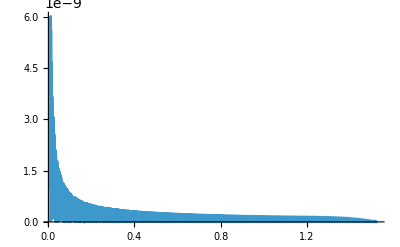

```mathematica
Plot[Abs[δrODEPBO[r]-corrPlungeBoundOrbit["δrpar"][r]],{r,1/100,r3g},PlotRange->All]
```

```mathematica
δtODEPBO=δt/.First@NDSolve[{δt'[r]==-(corrPlungeBoundOrbit["δvtpar"][r]-corrPlungeBoundOrbit["δΥrhat"]corrPlungeBoundOrbit["vtg"][r])/corrPlungeBoundOrbit["vrg"][r],δt[r3g-10^(-10)]==corrPlungeBoundOrbit["δtpar"][r3g-10^(-10)]},δt,{r,rp+10^(-3),r3g-10^(-10)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

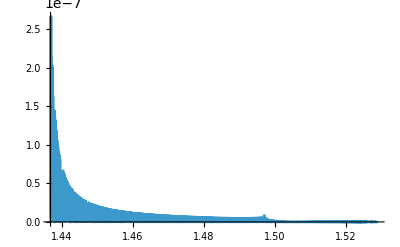

```mathematica
Plot[Abs[δtODEPBO[r]-corrPlungeBoundOrbit["δtpar"][r]],{r,rp+10^(-3),r3g},PlotRange->All]
```

```mathematica
δϕODEPBO=δϕ/.First@NDSolve[{δϕ'[r]==-(corrPlungeBoundOrbit["δvϕpar"][r]-corrPlungeBoundOrbit["δΥrhat"]corrPlungeBoundOrbit["vϕg"][r])/corrPlungeBoundOrbit["vrg"][r],δϕ[r3g-10^(-10)]==corrPlungeBoundOrbit["δϕpar"][r3g-10^(-10)]},δϕ,{r,rp+10^(-3),r3g-10^(-10)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->22,PrecisionGoal->20,AccuracyGoal->20];
```

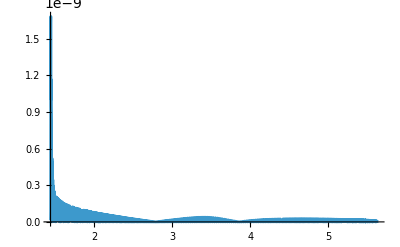

```mathematica
Plot[Abs[δϕODEPBO[r]-corrPlungeBoundOrbit["δϕpar"][r]],{r,rp+10^(-3),r3g},PlotRange->All]
```

## Regular gauge - retrograde

### Calculation orbits

IMPORTANT NOTE: the input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aPlungeBoundOrbit=0.9`50;
eccPlungeBoundOrbit=0.7`50;
xPlungeBoundOrbit=-1;
```

```mathematica
pPlungeBoundOrbit=KerrGeoSeparatrix[aPlungeBoundOrbit,eccPlungeBoundOrbit,xPlungeBoundOrbit]+1;
```

```mathematica
rp=1+√(1-aPlungeBoundOrbit^2);
rm=1-√(1-aPlungeBoundOrbit^2);
```

```mathematica
corrPlungeBoundOrbit=KerrNearEqSpinOrbitCorrFEPlungeBoundOrbit[aPlungeBoundOrbit,pPlungeBoundOrbit,eccPlungeBoundOrbit,xPlungeBoundOrbit];
```

Starting point of plunges related to bound orbits: r_(3g)=2/(1-E_g^2)-(r_(1g)+r_(2g))

```mathematica
r3g=2/(1-corrPlungeBoundOrbit["Eg"]^2)-(pPlungeBoundOrbit/(1-eccPlungeBoundOrbit)+pPlungeBoundOrbit/(1+eccPlungeBoundOrbit));
```

### Numerical solutions equations of motion vs analytic results

```mathematica
δrODEPBO=δr/.First@NDSolve[{δr'[r]==corrPlungeBoundOrbit["δvrpar"][r]/corrPlungeBoundOrbit["vrg"][r]-corrPlungeBoundOrbit["δΥrhat"],δr[r3g-10^(-10)]==corrPlungeBoundOrbit["δrpar"][r3g-10^(-10)]},δr,{r,1/100,r3g-10^(-10)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

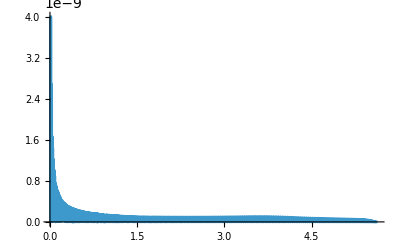

```mathematica
Plot[Abs[δrODEPBO[r]-corrPlungeBoundOrbit["δrpar"][r]],{r,1/100,r3g},PlotRange->All]
```

```mathematica
δtODEPBO=δt/.First@NDSolve[{δt'[r]==-(corrPlungeBoundOrbit["δvtpar"][r]-corrPlungeBoundOrbit["δΥrhat"]corrPlungeBoundOrbit["vtg"][r])/corrPlungeBoundOrbit["vrg"][r],δt[r3g-10^(-10)]==corrPlungeBoundOrbit["δtpar"][r3g-10^(-10)]},δt,{r,rp+10^(-3),r3g-10^(-10)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->22,PrecisionGoal->20,AccuracyGoal->20];
```

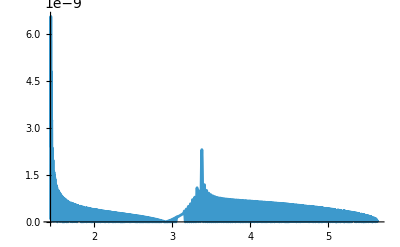

```mathematica
Plot[Abs[δtODEPBO[r]-corrPlungeBoundOrbit["δtpar"][r]],{r,rp+10^(-3),r3g},PlotRange->All]
```

```mathematica
δϕODEPBO=δϕ/.First@NDSolve[{δϕ'[r]==-(corrPlungeBoundOrbit["δvϕpar"][r]-corrPlungeBoundOrbit["δΥrhat"]corrPlungeBoundOrbit["vϕg"][r])/corrPlungeBoundOrbit["vrg"][r],δϕ[r3g-10^(-10)]==corrPlungeBoundOrbit["δϕpar"][r3g-10^(-10)]},δϕ,{r,rp+10^(-3),r3g-10^(-10)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->22,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[δϕODEPBO[r]-corrPlungeBoundOrbit["δϕpar"][r]],{r,rp+10^(-3),r3g},PlotRange->All]
```

-Graphics-

## Critical plunge

## Regular gauge - prograde

### Calculation orbits

IMPORTANT NOTE: the input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aCritplunge=0.9`50;
eccCritplunge=0.45`50;
xCritplunge=1;
```

```mathematica
pCritplunge=KerrGeoSeparatrix[aCritplunge,eccCritplunge,xCritplunge]
```

2.77433156421648935787406408054133207855903537732

```mathematica
rp=1+√(1-aCritplunge^2);
rm=1-√(1-aCritplunge^2);
```

```mathematica
r2g=pCritplunge/(1+eccCritplunge);
```

Critical plunge

```mathematica
AbsoluteTiming[corrCritplunge=KerrNearEqSpinOrbitCorrFECritPlunge[aCritplunge,pCritplunge,eccCritplunge,xCritplunge];]
```

{0.00312,Null}

### Numerical solutions equations of motion vs analytic results

```mathematica
δrODECritPlunge=δr/.First@NDSolve[{δr'[r]==corrCritplunge["δvrpar"][r]/corrCritplunge["vrg"][r]-corrCritplunge["δΥrhat"],δr[r2g-10^(-10)]==corrCritplunge["δrpar"][r2g-10^(-10)]},δr,{r,1/100,r2g-10^(-10)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

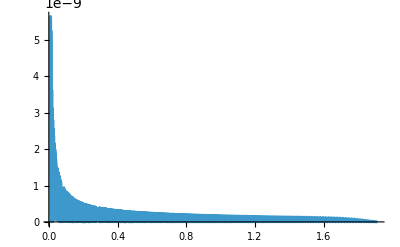

```mathematica
Plot[Abs[δrODECritPlunge[r]-corrCritplunge["δrpar"][r]],{r,1/100,r2g-10^(-10)},PlotRange->All]
```

```mathematica
δtODECritplunge=δt/.First@NDSolve[{δt'[r]==(corrCritplunge["δvtpar"][r]-corrCritplunge["δΥrhat"]corrCritplunge["vtg"][r])/corrCritplunge["vrg"][r],δt[r2g-10^(-3)]==corrCritplunge["δtpar"][r2g-10^(-3)]},δt,{r,rp+10^(-3),r2g-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

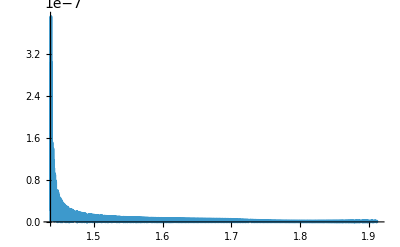

```mathematica
Plot[Abs[δtODECritplunge[r]-corrCritplunge["δtpar"][r]],{r,rp+10^(-3),r2g-10^(-3)},PlotRange->All]
```

```mathematica
δϕODECritplunge=δϕ/.First@NDSolve[{δϕ'[r]==(corrCritplunge["δvϕpar"][r]-corrCritplunge["δΥrhat"]corrCritplunge["vϕg"][r])/corrCritplunge["vrg"][r],δϕ[r2g-10^(-3)]==corrCritplunge["δϕpar"][r2g-10^(-3)]},δϕ,{r,rp+10^(-3),r2g-10^(-3)},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

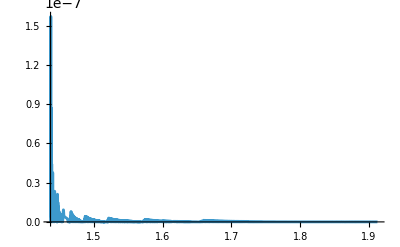

```mathematica
Plot[Abs[δϕODECritplunge[r]-corrCritplunge["δϕpar"][r]],{r,rp+10^(-3),r2g-10^(-3)},PlotRange->All]
```

### Plot to export

```mathematica
δϕODECritplunge0rm=δϕ/.First@NDSolve[{δϕ'[r]==(corrCritplunge["δvϕpar"][r]-corrCritplunge["δΥrhat"]corrCritplunge["vϕg"][r])/corrCritplunge["vrg"][r],δϕ[rm-10^(-3)]==corrCritplunge["δϕpar"][rm-10^(-3)]},δϕ,{r,10^(-2),rm-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->34,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
δϕODECritplungermrp=δϕ/.First@NDSolve[{δϕ'[r]==(corrCritplunge["δvϕpar"][r]-corrCritplunge["δΥrhat"]corrCritplunge["vϕg"][r])/corrCritplunge["vrg"][r],δϕ[rp-10^(-3)]==corrCritplunge["δϕpar"][rp-10^(-3)]},δϕ,{r,rm+10^(-3),rp-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->34,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
δϕODECritplungerpr2g=δϕ/.First@NDSolve[{δϕ'[r]==(corrCritplunge["δvϕpar"][r]-corrCritplunge["δΥrhat"]corrCritplunge["vϕg"][r])/corrCritplunge["vrg"][r],δϕ[r2g-10^(-3)]==corrCritplunge["δϕpar"][r2g-10^(-3)]},δϕ,{r,rp+10^(-3),r2g-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->34,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
plotdiffδϕCrit0rm=LogPlot[Abs[corrCritplunge[ "δϕpar"][r]-δϕODECritplunge0rm[r]],{r,10^(-2),rm-10^(-3)},LabelStyle->{FontSize->20,FontFamily->"Times",Black},PlotStyle->Red,PlotRange->{{0,r2g-1/100},All},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,26],Style["|δϕ_analytic^Critical-δϕ_num^Critical|",Black,26]},ImageMargins->5,ImagePadding->{{100, 20}, {Automatic,10}},ImageSize->600,WorkingPrecision->24];
```

```mathematica
plotdiffδϕCritrmrp=LogPlot[Abs[corrCritplunge[ "δϕpar"][r]-δϕODECritplungermrp[r]],{r,rm+10^(-3),rp-10^(-3)},LabelStyle->{FontSize->20,FontFamily->"Times",Black},PlotStyle->Red,PlotRange->{{0,r2g-1/100},All},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,26],Style["|δϕ_analytic^Critical-δϕ_num^Critical|",Black,26]},ImageMargins->5,ImagePadding->{{100, 20}, {Automatic,10}},ImageSize->600,WorkingPrecision->24];
```

```mathematica
plotdiffδϕCritrpr2g=LogPlot[Abs[corrCritplunge[ "δϕpar"][r]-δϕODECritplungerpr3g[r]],{r,rp+10^(-3),r2g-10^(-3)},LabelStyle->{FontSize->20,FontFamily->"Times",Black},PlotStyle->Red,PlotRange->{{0,r2g-1/100},All},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,26],Style["|δϕ_analytic^Critical-δϕ_num^Critical|",Black,26]},ImageMargins->5,ImagePadding->{{100, 20}, {Automatic,10}},ImageSize->600,WorkingPrecision->24];
```

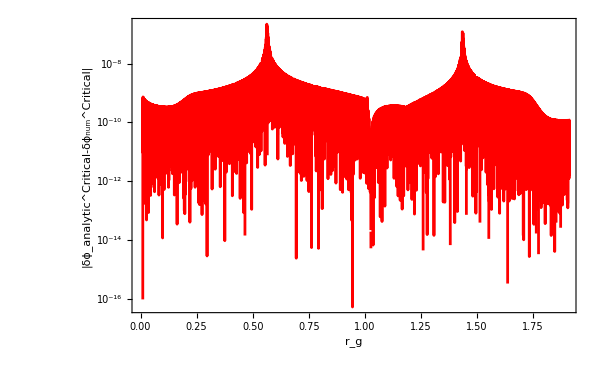

```mathematica
plotdiffδϕCrit=Show[plotdiffδϕCrit0rm,plotdiffδϕCritrmrp,plotdiffδϕCritrpr2g]
```

```mathematica
(*Export["numerical_checks_Critical_plunge.pdf",plotdiffδϕCrit]*)
```

## Regular gauge - retrograde

### Calculation orbits

IMPORTANT NOTE: the input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aCritplunge=0.9`50;
eccCritplunge=0.45`50;
xCritplunge=-1;
```

```mathematica
pCritplunge=KerrGeoSeparatrix[aCritplunge,eccCritplunge,xCritplunge]
```

9.94962412521538647758316932741738178793769289441

```mathematica
rp=1+√(1-aCritplunge^2);
rm=1-√(1-aCritplunge^2);
```

```mathematica
r2g=pCritplunge/(1+eccCritplunge);
```

Critical plunge

```mathematica
AbsoluteTiming[corrCritplunge=KerrNearEqSpinOrbitCorrFECritPlunge[aCritplunge,pCritplunge,eccCritplunge,xCritplunge];]
```

{0.004849,Null}

### Numerical solutions equations of motion vs analytic results

```mathematica
δrODECritPlunge=δr/.First@NDSolve[{δr'[r]==corrCritplunge["δvrpar"][r]/corrCritplunge["vrg"][r]-corrCritplunge["δΥrhat"],δr[r2g-10^(-10)]==corrCritplunge["δrpar"][r2g-10^(-10)]},δr,{r,1/100,r2g-10^(-10)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

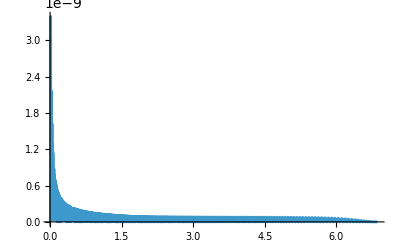

```mathematica
Plot[Abs[δrODECritPlunge[r]-corrCritplunge["δrpar"][r]],{r,1/100,r2g-10^(-10)},PlotRange->All]
```

```mathematica
δtODECritplunge=δt/.First@NDSolve[{δt'[r]==(corrCritplunge["δvtpar"][r]-corrCritplunge["δΥrhat"]corrCritplunge["vtg"][r])/corrCritplunge["vrg"][r],δt[r2g-10^(-3)]==corrCritplunge["δtpar"][r2g-10^(-3)]},δt,{r,rp+10^(-3),r2g-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

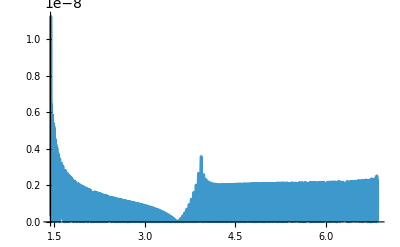

```mathematica
Plot[Abs[δtODECritplunge[r]-corrCritplunge["δtpar"][r]],{r,rp+10^(-3),r2g-10^(-3)},PlotRange->All]
```

```mathematica
δϕODECritplunge=δϕ/.First@NDSolve[{δϕ'[r]==(corrCritplunge["δvϕpar"][r]-corrCritplunge["δΥrhat"]corrCritplunge["vϕg"][r])/corrCritplunge["vrg"][r],δϕ[r2g-10^(-3)]==corrCritplunge["δϕpar"][r2g-10^(-3)]},δϕ,{r,rp+10^(-3),r2g-10^(-3)},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

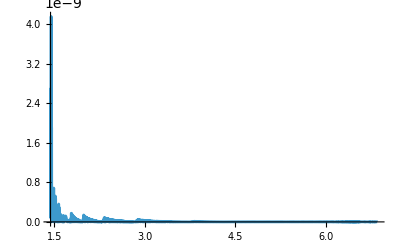

```mathematica
Plot[Abs[δϕODECritplunge[r]-corrCritplunge["δϕpar"][r]],{r,rp+10^(-3),r2g-10^(-3)},PlotRange->All]
```

## ISCO plunge

## Regular gauge - prograde

### Calculation orbits

IMPORTANT NOTE: the input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aISCOplunge=0.9`45;
xISCOplunge=1;
```

```mathematica
rISCO=KerrGeoSeparatrix[aISCOplunge,0,xISCOplunge]
```

2.320883041761887246790086191922686088978602

```mathematica
rp=1+√(1-aISCOplunge^2);
rm=1-√(1-aISCOplunge^2);
```

ISCO plunge

```mathematica
AbsoluteTiming[corrISCOplunge=KerrNearEqSpinOrbitCorrISCOPlunge[aISCOplunge,xISCOplunge];]
```

{0.002403,Null}

### Numerical solutions equations of motion vs analytic results

```mathematica
δrODEISCOPlunge=δr/.First@NDSolve[{δr'[r]==corrISCOplunge["δvrpar"][r]/corrISCOplunge["vrg"][r]-corrISCOplunge["δΥrhat"],δr[rISCO-10^(-10)]==corrISCOplunge["δrpar"][rISCO-10^(-10)]},δr,{r,1/100,rISCO-10^(-10)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->20,PrecisionGoal->15,AccuracyGoal->15];
```

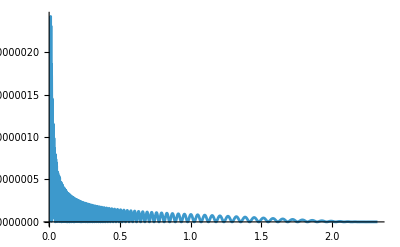

```mathematica
Plot[Abs[δrODEISCOPlunge[r]-corrISCOplunge["δrpar"][r]],{r,1/100,rISCO-10^(-10)},PlotRange->All]
```

```mathematica
δtODEISCOplunge=δt/.First@NDSolve[{δt'[r]==(corrISCOplunge["δvtpar"][r]-corrISCOplunge["δΥrhat"]corrISCOplunge["vtg"][r])/corrISCOplunge["vrg"][r],δt[rISCO-10^(-3)]==corrISCOplunge["δtpar"][rISCO-10^(-3)]},δt,{r,rp+10^(-3),rISCO-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

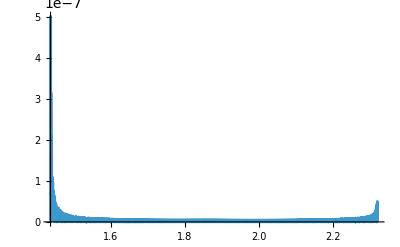

```mathematica
Plot[Abs[δtODEISCOplunge[r]-corrISCOplunge["δtpar"][r]],{r,rp+10^(-3),rISCO-10^(-3)},PlotRange->All]
```

```mathematica
δϕODEISCOplunge=δϕ/.First@NDSolve[{δϕ'[r]==(corrISCOplunge["δvϕpar"][r]-corrISCOplunge["δΥrhat"]corrISCOplunge["vϕg"][r])/corrISCOplunge["vrg"][r],δϕ[rISCO-10^(-3)]==corrISCOplunge["δϕpar"][rISCO-10^(-3)]},δϕ,{r,rp+10^(-3),rISCO-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

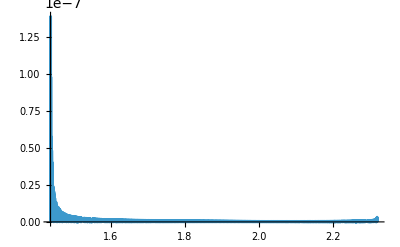

```mathematica
Plot[Abs[δϕODEISCOplunge[r]-corrISCOplunge["δϕpar"][r]],{r,rp+10^(-3),rISCO-10^(-3)},PlotRange->All]
```

### Plot to export

```mathematica
δϕODEISCOplunge0rm=δϕ/.First@NDSolve[{δϕ'[r]==(corrISCOplunge["δvϕpar"][r]-corrISCOplunge["δΥrhat"]corrISCOplunge["vϕg"][r])/corrISCOplunge["vrg"][r],δϕ[rm-10^(-3)]==corrISCOplunge["δϕpar"][rm-10^(-3)]},δϕ,{r,10^(-2),rm-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->34,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
δϕODEISCOplungermrp=δϕ/.First@NDSolve[{δϕ'[r]==(corrISCOplunge["δvϕpar"][r]-corrISCOplunge["δΥrhat"]corrISCOplunge["vϕg"][r])/corrISCOplunge["vrg"][r],δϕ[rp-10^(-3)]==corrISCOplunge["δϕpar"][rp-10^(-3)]},δϕ,{r,rm+10^(-3),rp-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->34,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
δϕODEISCOplungerpr3g=δϕ/.First@NDSolve[{δϕ'[r]==(corrISCOplunge["δvϕpar"][r]-corrISCOplunge["δΥrhat"]corrISCOplunge["vϕg"][r])/corrISCOplunge["vrg"][r],δϕ[rISCO-10^(-3)]==corrISCOplunge["δϕpar"][rISCO-10^(-3)]},δϕ,{r,rp+10^(-3),rISCO-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->34,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
plotdiffδϕISCO0rm=LogPlot[Abs[corrISCOplunge[ "δϕpar"][r]-δϕODEISCOplunge0rm[r]],{r,10^(-2),rm-10^(-3)},LabelStyle->{FontSize->20,FontFamily->"Times",Black},PlotStyle->Red,PlotRange->{{0,rISCO-1/100},All},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,26],Style["|δϕ_analytic^ISCO-δϕ_num^ISCO|",Black,26]},ImageMargins->5,ImagePadding->{{100, 20}, {Automatic,10}},ImageSize->600];
```

```mathematica
plotdiffδϕISCOrmrp=LogPlot[Abs[corrISCOplunge[ "δϕpar"][r]-δϕODEISCOplungermrp[r]],{r,rm+10^(-3),rp-10^(-3)},LabelStyle->{FontSize->20,FontFamily->"Times",Black},PlotStyle->Red,PlotRange->{{0,rISCO-1/100},All},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,26],Style["|δϕ_analytic^ISCO-δϕ_num^ISCO|",Black,26]},ImageMargins->5,ImagePadding->{{100, 20}, {Automatic,10}},ImageSize->600];
```

```mathematica
plotdiffδϕISCOrpr3g=LogPlot[Abs[corrISCOplunge[ "δϕpar"][r]-δϕODEISCOplungerpr3g[r]],{r,rp+10^(-3),rISCO-10^(-3)},LabelStyle->{FontSize->20,FontFamily->"Times",Black},PlotStyle->Red,PlotRange->{{0,rISCO-1/100},All},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_g",Black,26],Style["|δϕ_analytic^ISCO-δϕ_num^ISCO|",Black,26]},ImageMargins->5,ImagePadding->{{100, 20}, {Automatic,10}},ImageSize->600];
```

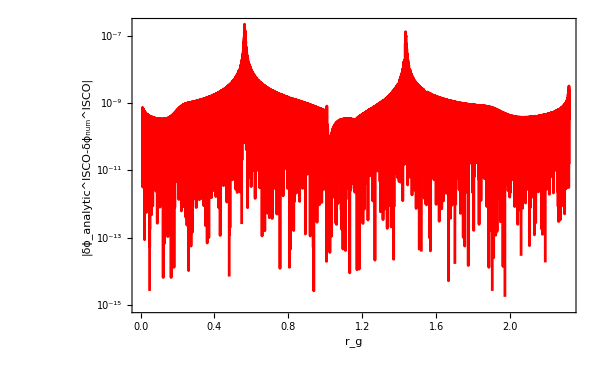

```mathematica
plotdiffδϕISCO=Show[plotdiffδϕISCO0rm,plotdiffδϕISCOrmrp,plotdiffδϕISCOrpr3g]
```

```mathematica
Export["numerical_checks_ISCO_plunge.pdf",plotdiffδϕISCO]
```

numerical_checks_ISCO_plunge.pdf

## Regular gauge - retrograde

### Calculation orbits

IMPORTANT NOTE: the input of the following functions are:

- primary spin “a”
- semi-latus rectum “p”
- eccentricity “e”
- direction of the orbits “x” : +1 prograde, -1 retrograde

Location of the geodesic separatrix

```mathematica
aCritplunge=0.9`45;
eccCritplunge=0.45`45;
xISCOplunge=-1;
```

```mathematica
pCritplunge=KerrGeoSeparatrix[aCritplunge,eccCritplunge,xISCOplunge]
```

9.949624125215386477583169327417381787937693

```mathematica
rp=1+√(1-aCritplunge^2);
rm=1-√(1-aCritplunge^2);
```

```mathematica
r2g=pCritplunge/(1+eccCritplunge);
```

Critical plunge

```mathematica
AbsoluteTiming[corrCritplunge=KerrNearEqSpinOrbitCorrRCritPlunge[aCritplunge,pCritplunge,eccCritplunge,xISCOplunge];]
```

{0.00844,Null}

### Numerical solutions equations of motion vs analytic results

```mathematica
δrODEISCOPlunge=δr/.First@NDSolve[{δr'[r]==corrISCOplunge["δvrpar"][r]/corrISCOplunge["vrg"][r]-corrISCOplunge["δΥrhat"],δr[rISCO-10^(-10)]==corrISCOplunge["δrpar"][rISCO-10^(-10)]},δr,{r,1/100,rISCO-10^(-10)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->20,PrecisionGoal->15,AccuracyGoal->15];
```

```mathematica
Plot[Abs[δrODEISCOPlunge[r]-corrISCOplunge["δrpar"][r]],{r,1/100,rISCO-10^(-10)},PlotRange->All]
```

-Graphics-

```mathematica
δtODEISCOplunge=δt/.First@NDSolve[{δt'[r]==(corrISCOplunge["δvtpar"][r]-corrISCOplunge["δΥrhat"]corrISCOplunge["vtg"][r])/corrISCOplunge["vrg"][r],δt[rISCO-10^(-3)]==corrISCOplunge["δtpar"][rISCO-10^(-3)]},δt,{r,rp+10^(-3),rISCO-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[δtODEISCOplunge[r]-corrISCOplunge["δtpar"][r]],{r,rp+10^(-3),rISCO-10^(-3)},PlotRange->All]
```

-Graphics-

```mathematica
δϕODEISCOplunge=δϕ/.First@NDSolve[{δϕ'[r]==(corrISCOplunge["δvϕpar"][r]-corrISCOplunge["δΥrhat"]corrISCOplunge["vϕg"][r])/corrISCOplunge["vrg"][r],δϕ[rISCO-10^(-3)]==corrISCOplunge["δϕpar"][rISCO-10^(-3)]},δϕ,{r,rp+10^(-3),rISCO-10^(-3)},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}},WorkingPrecision->24,PrecisionGoal->20,AccuracyGoal->20];
```

```mathematica
Plot[Abs[δϕODEISCOplunge[r]-corrISCOplunge["δϕpar"][r]],{r,rp+10^(-3),rISCO-10^(-3)},PlotRange->All]
```

-Graphics-